```mathematica
Manipulate[ContourPlot[Tanh[((x-xc)^2+y^2-1^2)/0.1],{x,0,5},{y,0,5}, PlotPoints->100], {xc, 0,5,0.1}]
```

```mathematica
Manipulate[Plot3D[0.5(1-Tanh[((x-xc)^2+y^2-1^2)/0.01]),{x,0,5},{y,0,5}, PlotRange->All], {xc, 0,5,0.1}]
```

```mathematica
Manipulate[Plot3D[0.5(1-Tanh[((x-xc)^2+y^2-1^2)/0.01]),{x,0,5},{y,0,5}, PlotRange->All], {xc, 0,5,0.1}]
```

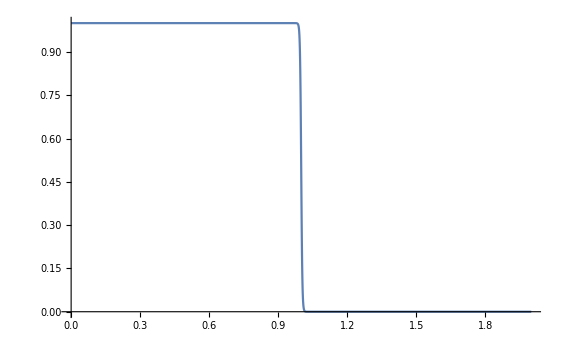

```mathematica
Plot[0.5*(1-Tanh[(y^2-1^2)/0.01]), {y,0,2}]
```

```mathematica
NSolve[0.5*(1-Tanh[(y^2-1^2)/0.1])==0.99,y]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{y→-0.877635},{y→-0.877635},{y→0.877635},{y→0.877635}}

```mathematica
Solve[0.5*(1-Tanh[((1-hmin)^2-1^2)/delta])==0.99,delta]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{delta→0.000849672},{delta→0.000849672}}

```mathematica
0.5*(1-Tanh[((1+2*hmin)^2-1^2)/0.0008505017227174922])
```

0.000101563

```mathematica
0.5*(1-Tanh[((1-hmin)^2-1^2)/0.00866])
```

```mathematica
(2*hmin*0.0625+hmin^2)/ArcTanh[1- 2*0.01]
```

0.0000535455

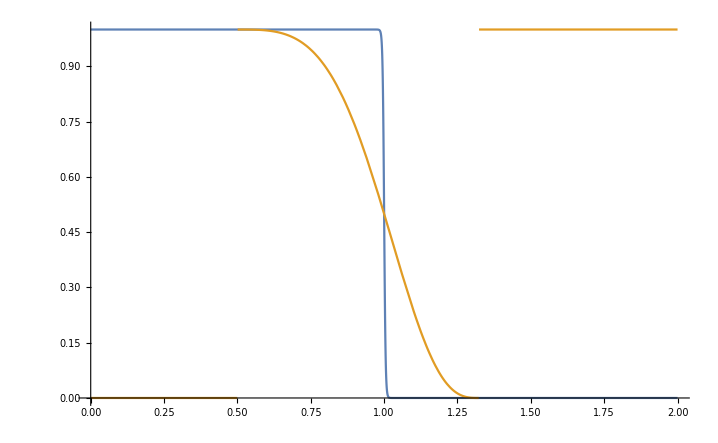

```mathematica
d=1.5;hmin=1/2^1;
Indicator[x_]:=If[Abs[x]≤ hmin*d,0.5*(1+x/(d*hmin)+1/Pi Sin[(Pi*x)/(d*hmin)] ),If[x≤- hmin*d, 1,0] ]
Plot[{0.5*(1-Tanh[(y^2-1^2)/0.01]),1-Indicator[y^2-1]}, {y,0,2}]
```